## Visible Algebra II

### Introduction

This Mathematica notebook is licensed under a  
It creates the demonstrations used in my post Visible Algebra II.

I hope anyone interested will feel free to improve this work and to use it in their own publications and coursework.

### Definitions

```mathematica
preop[x_,loc_]:=Text[Framed[Style[x,Medium,FontFamily->"Arial"],Background->White],loc]
```

```mathematica
preop["x",{0,1}]
```

Text[x,{0,1}]

```mathematica
Text["x",{0,1}]
```

Text[x,{0,1}]

```mathematica
DarkGreen:=RGBColor[0,.6,0]
```

```mathematica
Framed[Style[42555,Medium,FontFamily->"Arial"],ImageSize->45,Background->White]
```

42555

```mathematica
fixedop[x_,loc_,width_]:=Text[Framed[Style[x,Medium,FontF;amily->"Arial"],ImageSize->width,Background->White],loc]
```

```mathematica
fixedop[3.13,{0,0},100]
```

Text[3.13,{0,0}]

```mathematica
op[x_,loc_]:=preop[x,loc];op[x_,loc_,width_]:=fixedop[x,loc,width]
```

```mathematica
lab[x_,loc_]:=Text[Style[x,Small,FontFamily->"Arial",Background->White],loc]
```

```mathematica
edge[op1_,op2_,sf_]:=Arrow[{op1,op2},Scaled[sf]]
```

```mathematica
edge[op1_,op2_]:=edge[op1,op2,0]
```

```mathematica
ledge[op1_,op2_,label_]:=Sequence[edge[op1,op2],lab[label,.5(op1+op2)]]
```

```mathematica
fixedop[{Style["Power\n",LineSpacing->{0,1}],PaddedForm[255,4]}//TableForm,{0,0},50]
```

Text[Power

  255,{0,0}]

```mathematica
fixedop[x_,loc_,width_]:=Text[Framed[Style[x,Medium,FontFamily->"Arial"],ImageSize->width,Background->White],loc]
```

### Operations

```mathematica
Show[
Graphics[
{Arrowheads[0],
ledge[{0,0},{-1,-1},"base"],
ledge[{0,0},{1,-1},"exp"],
op["Power",{0,0}],
op[a,{-1,-1}],
op[b,{1,-1}]
},
ImageSize->100, AspectRatio->.7,PlotRange->{{-2,2},Automatic}
]
]
```

-Graphics-

```mathematica
Manipulate[Show[
Graphics[
{Arrowheads[0],
ledge[{0,0},{-2,-2},"base"],
ledge[{0,0},{2,-2},"exp"],
fixedop[PaddedForm[a^b,4]"Power",{0,0},60],
fixedop[a,{-2,-2},50],
fixedop[b,{2,-2},50]
},
ImageSize->150, AspectRatio->.8,PlotRange->{{-4.5,4.5},Automatic}
]
],{{a,2},.01,4},{{b,3},.01,4},Paneled->False,ControlPlacement->Bottom]
```

```mathematica
Manipulate[Show[
Graphics[
{Arrowheads[0],
ledge[{0,0},{-2,-2},"base"],
ledge[{0,0},{2,-2},"exp"],
op[{Style["Power\n",LineSpacing->{0,1}],PaddedForm[a^b,4]}//TableForm,{0,0},55],
op[a,{-2,-2},45],
op[b,{2,-2},45]
},
ImageSize->150, AspectRatio->.8,PlotRange->{{-4.5,4.5},Automatic}
]
],{{a,2},.01,4},{{b,3},.01,4},Paneled->False,ControlPlacement->Bottom,SaveDefinitions->True]
```

```mathematica
Manipulate[Show[
Graphics[
{Arrowheads[0],
ledge[{0,0},{-2,-2},"given"],
ledge[{0,0},{2,-2},"take"],
op[{Style["Subtract\n",LineSpacing->{0,1}],PaddedForm[a-b,4]}//TableForm,{0,0},60],
op[a,{-2,-2},50],
op[b,{2,-2},50]
},
ImageSize->150, AspectRatio->.8,PlotRange->{{-4.5,4.5},Automatic}
]
],{{a,2},-4,4},{{b,3},-4,4},Paneled->False,ControlPlacement->Bottom,SaveDefinitions->True]
```

### Associative law

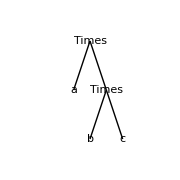

```mathematica
Show[
Graphics[
{Arrowheads[0],
edge[{0,0},{-1,-1}],
edge[{0,0},{1,-1}],
edge[{1,-1},{0,-2}],
edge[{1,-1},{2,-2}],
op["Times",{0,0}],
op[a,{-1,-1}],
op["Times",{1,-1}],
op[b,{0,-2}],
op[c,{2,-2}] 
},
ImageSize->180, AspectRatio->1,PlotRange->{{-4.5,4.5},{-2.5,.5}}
]]
```

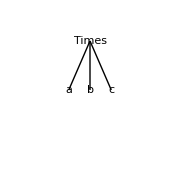

```mathematica
Show[
Graphics[
{Arrowheads[0],
edge[{0,0},{-1.3,-1}],
edge[{0,0},{0,-1}],
edge[{0,0},{1.3,-1}],
op["Times",{0,0}],
op[a,{-1.3,-1}],
op[b,{0,-1}] ,op[c,{1.3,-1}]
},
ImageSize->180, AspectRatio->1,PlotRange->{{-4.5,4.5},{-2.5,.5}}
]]
```

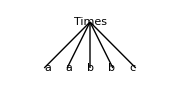

```mathematica
Show[
Graphics[
{Arrowheads[0],
edge[{0,0},{-2.8,-1}],
edge[{0,0},{-1.4,-1}],
edge[{0,0},{0,-1}],
edge[{0,0},{1.4,-1}],
edge[{0,0},{2.8,-1}],
op["Times",{0,0}],
op[a,{-2.6,-1}],
op[a,{-1.3,-1}],
op[b,{0,-1}] ,
op[b,{1.3,-1}],
op[c,{2.6,-1}]
},
ImageSize->180, AspectRatio->1/2,PlotRange->{{-4.5,4.5},{-1.3,.3}}
]]
```

```mathematica
Manipulate[
Show[
Graphics[
{Arrowheads[0],
edge[{0,0},p-{.2,0}],
edge[{0,0},q],
edge[{0,0},r],
edge[{0,0},s],
edge[{0,0},t],
op["Times",{0,0}],
op[a,p],
op[a,q],
op[b,r] ,
op[b,s],
op[c,t]
},
ImageSize->160, AspectRatio->1.4,PlotRange->{{-4.5,4.5},{-1.8,.6}}
]
],{{p,{-2.6,-1}},Locator,Appearance->None},{{q,{-1.3,-1}},Locator,Appearance->None},{{r,{0,-1}},Locator,Appearance->None},{{s,{1.3,-1}},Locator,Appearance->None},{{t,{2.6,-1}},Locator,Appearance->None},Paneled->False, SaveDefinitions->True
]
```

```mathematica
Manipulate[
Show[
Graphics[
{Arrowheads[0],
edge[{0,0},p-{.2,0}],
edge[{0,0},q],
edge[{0,0},r],
edge[{0,0},s],
edge[{0,0},t],
op["Times",{0,0}],
op[a,p],
op[a,q],
op[b,r] ,
op[b,s],
op[c,t]
},
ImageSize->160, AspectRatio->1.4,PlotRange->{{-4.5,4.5},{-1.8,.6}}
]
],{{p,{-2.6,-1}},Locator,Appearance->None},{{q,{-1.3,-1}},Locator,Appearance->None},{{r,{0,-1}},Locator,Appearance->None},{{s,{1.3,-1}},Locator,Appearance->None},{{t,{2.6,-1}},Locator,Appearance->None},Paneled->False
]
```

```mathematica
{Style["Plus\n",LineSpacing->{0,1}],
PaddedForm[Style[h w.5Pi 0.5w^2,Blue],4]
}//TableForm],{0,0},55],
```

```mathematica
Manipulate[
Show[
Graphics[
{Arrowheads[0],
edge[{0,0},{-2.8,-1}],
edge[{0,0},{-1.4,-1}],
edge[{0,0},{0,-1}],
edge[{0,0},{1.4,-1}],
edge[{0,0},{2.8,-1}],
If[evaluated,op[Style[a+b+c+a+b,Blue],{0,0}],op["Plus",{0,0}]],
op[PaddedForm[{Style["\ a\n",LineSpacing->{0,1}],Style[a,Blue]}//TableForm,3],{-2.6,-1}],
op[b,{-1.3,-1}],
op[c,{0,-1}] ,
op[a,{1.3,-1}],
op[c,{2.6,-1}]
},
ImageSize->180, AspectRatio->1/2,PlotRange->{{-4.5,4.5},{-1.3,.3}}
]],{evaluated,{False,True}},{{a,2},0,9.9,.1},{{b,3},0,9.9,.1},{{c,4},0,9.9,.1}]
```

```mathematica
Manipulate[
Show[
Graphics[
{Arrowheads[0],
edge[{0,0},{-1-.3d,-1}],
edge[{0,0},{1-d,-1+d}],
edge[{1-d,-1+d},{0,-2+d}],
edge[{1-d,-1+d},{2-.6d,-2+d}],
op["Times",{0,0}],
op[a,{-1-.3d,-1}],
op["Times",{1-d,-1+d}],
op[b,{0,-2+d}],
op[c,{2-.6d,-2+d}] 
},
ImageSize->180, AspectRatio->1,PlotRange->{{-4.5,4.5},{-2.5,.5}}
]
],{{d,0},0,1},Paneled->False,ControlPlacement->Bottom]
```

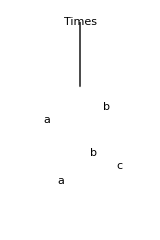

```mathematica
Graphics[{Opacity[1],Black,
Arrowheads[0],
edge[{0,-1},{0,0}],
op["Times",{0,0}],White,Opacity[1],EdgeForm[Thin],Disk[{0,-1},1/2],Black,
Text[a, {-.25,-.75}],Text[a, {-.15,-1.22}],Text[b, {.2,-.65}],Text[b, {.1,-1}],Text[c, {.3,-1.1}]
},ImagePadding->30,
ImageSize->160, AspectRatio->3/2,PlotRange->{{-1/2,1/2},{-3/2,0}}
]
```

```mathematica
{$43000,$54000,$43000,$76000,$54000}//TableForm
```

$43000
$54000
$43000
$76000
$54000

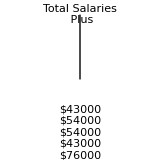

```mathematica
Graphics[{Opacity[1],Black,
Arrowheads[0],
edge[{0,-1},{0,0}],
op["Total Salaries\n Plus",{0,0}],White,Opacity[1],EdgeForm[Thin],Rectangle[{-.2,-.5},{.2,-1.25}],Black,
Text[{$43000,$54000,$54000,$43000,$76000}//TableForm,{0,-.9}]
},ImagePadding->30,
ImageSize->160, AspectRatio->1,PlotRange->{{-1/2,1/2},{-1,0}}
]
```

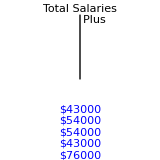

```mathematica
Graphics[{Opacity[1],Black,
Arrowheads[0],
edge[{0,-1},{0,0}],
op[Column[{"Total Salaries",Style["        Plus",Blue]},Spacings->.4],{0,0}],White,Opacity[1],EdgeForm[Thin],Rectangle[{-.2,-.5},{.2,-1.25}],Black,
Text[Style[{$43000,$54000,$54000,$43000,$76000}//TableForm,Blue],{0,-.9}]
},ImagePadding->30,
ImageSize->160, AspectRatio->1,PlotRange->{{-1/2,1/2},{-1,0}}
]
```